## Insertion Device Functions (last update: 02/21)

```mathematica
(* 	
	Conferir:;
- Posição cassetes EPU);
- Parametro K calculado com campo total no Erro de Fase;


   Adicionar:;
- Adicionar Simetria no processo de importação de magnetização;
- Help das funções;
- Checks internos das funções; 
- Parâmetros opcionais;

*)
```

## Principal Functions

### Load Radia

```mathematica
<<Radia`;
RadPlot3DOptions[];
radUtiDelAll[]; (*Erase all previous elements*)
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

### BlockGeometry

```mathematica
idBlockGeometry[checkgeo_]:=(
Module[{geo1,geo2,geo3},

(*Geo A1, Delta 52.5*)
If[checkgeo==1,
geo1={{-21.5,-50},{21.5,-50},{22.5,-49},{22.5,-41.8},{16.794,-37.654},{-16.794,-37.654},{-22.5,-41.8},{-22.5,-49}};
geo2={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo3={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

If[checkgeo==2,
geo1={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo2={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

Return[{geo1,geo2,geo3}]
];
)
```

### cassetteDraw

```mathematica
cassetteDraw::usage = "magnetizations = Lista das magnetizações dos blocos de um cassete (lista de tamanho n); blockGeo = {geo1,geo2,geo3}; 
termination = {{lista de magnetizacoes na entrada}, {lista de espessuras na entrada}, {lista de espaçamentos na entrada},{lista de magnetizacoes na saída}, {lista de espessuras na saída}, {lista de espaçamentos na saída}}"; 


idCassetteDraw[magnetizations_,blockGeo_,posErrors_,termination_,periodL_,blockThick_,gap_,blockGap_,subdiv_]:=(
Module[{cassette,block,obj,obj1,obj2,obj3,blocknumber,vacodym745ap,termLength,i,j,parts,randomErrorY,randomErrorZ,longPos},

cassette=radObjCnt[{}];
parts=Length[blockGeo];
obj=ConstantArray[{},parts];
blocknumber=Length[magnetizations]+Length[termination[[1]]]+Length[termination[[4]]];

randomErrorY=Table[RandomVariate[NormalDistribution[0,1/3]],{i,1,blocknumber}]*posErrors[[1]];
randomErrorZ=Table[RandomVariate[NormalDistribution[0,1/3]],{i,1,Length[magnetizations]}]*posErrors[[2]];

(*===== Termination Front =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[1]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤1,
longPos=0,
longPos=longPos+0.5*termination[[2,i-1]]+termination[[3,i-1]]+0.5*termination[[2,i]];
];

(*Create the Block Object*)
For[j=1,j≤ parts,j++,
(*Extrude part*)
obj[[j]]=radObjThckPgn[longPos,termination[[2,i]],blockGeo[[j]],termination[[1,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.04,0.04},termination[[1,i]]];
radMatApl[block[[i]],vacodym745ap];

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];
];

(*===== Periods =====*)
block=ConstantArray[{},Length[magnetizations]];

For[i=1,i≤ Length[magnetizations],i++,
block[[i]]=radObjCnt[{}];

(*Block Position*)
If[i≤1,
longPos=longPos+0.5*termination[[2,-1]]+termination[[3,-1]]+0.5*blockThick;
,
longPos=longPos+blockThick+blockGap;
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,blockThick,blockGeo[[j]],magnetizations[[i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.04,0.04},magnetizations[[i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

(*===== Termination Back =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[4]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤ 1,
longPos=longPos+blockThick/2+termination[[6,1]]+termination[[5,1]]/2;
,
longPos=longPos+0.5*termination[[5,i-1]]+termination[[6,i]]+0.5*termination[[5,i]];
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,termination[[5,i]],blockGeo[[j]],termination[[4,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.04,0.04},termination[[1,i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

Return[cassette]
];
)
```

### IDDraw

```mathematica
idDraw[typeID_,blockGeo_,posErrors_,periodL_,blockThick_,gap_,blockGap_,nPeriods_,mode_,symmetry_,magnAmp_,magAmpError_,magTheta_,magImport_,fileName_,termType_,gap2_,magError_,subdiv_]:=(
Module[{device,cassette,mag,magnetizations,cassetteD,modeslist,phase,i,terminations,displacement,cassPos},
device=radObjCnt[{}];
cassette=ConstantArray[{},4];

(*Generate Magnetizations*)
If[magImport≥ 1,
magnetizations=idImportMag[typeID,nPeriods,fileName];
If[Length[magnetizations]<1,Return[Print["[Error] Can't generate the magnetizations list."]]];
,
magnetizations=idGenerateMag[typeID,nPeriods,symmetry,magnAmp,magAmpError,magTheta,periodL,blockThick,blockGap,magError];
];

(*Generate Terminations*)
terminations=idGenerateTerm[termType,blockThick,blockGap,periodL,magnAmp];

(*==== Generate Cassettes =====*)
For[i=1,i≤Length[magnetizations],i++,
cassette[[i]]=idCassetteDraw[magnetizations[[i]],blockGeo,posErrors,terminations[[i]],periodL,blockThick,gap,blockGap,subdiv];

(*Apply Gap*)
radTrfOrnt[cassette[[i]],radTrfTrsl[{0,0,-gap/2}]];

If[typeID=="DeltaUndulator",
(*Apply Phase*)
modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0},{-1/4,-1/4,0,0},{-1/4,0,0,-1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi/2]];
];

If[typeID=="PlanarUndulator",
(*Apply Phase*)
modeslist={{0,0},{0,-1/2},{0,-1/4},{0,1/2},{0,1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi]];
];

If[typeID=="EPU",
(*Apply Phase*)
modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Position*)
zdesloc=gap+50/2; ydesloc=gap2+22; a=Min[Flatten[blockGeo,1][[All,2]]];
cassPos={{0,-ydesloc,0},{0,ydesloc,0},{0,ydesloc,2*zdesloc},{0,-ydesloc,2*zdesloc}};

radTrfOrnt[cassette[[i]],radTrfTrsl[cassPos[[i]]]];
];


radObjAddToCnt[device,{cassette[[i]]}];
];

If[typeID=="DeltaUndulator",
(*Rotate ID*)
radTrfOrnt[device,radTrfRot[{0,0,0},{1,0,0},-Pi/4]];
];

(*Adjust Axis*)
radTrfOrnt[device,radTrfRot[{0,0,0},{0,1,0},-Pi/2]];
radTrfOrnt[device,radTrfRot[{0,0,0},{0,0,1},Pi/2]];

Return[device];
];
)
```

### GenerateMag

```mathematica
idGenerateMag[typeID_,nPeriods_,symmetry_,magnAmp_,magAmpError_,magTheta_,periodL_,blockThick_,blockGap_,magError_]:=(
Module[{mag,magnetization,j,i,termination,phi,theta,dmag},

(*===== ID Type =====*)
If[typeID=="DeltaUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="PlanarUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="EPU",
mag={{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}}};
];

(*===== Create Cassette Magnetizations =====*)
magnetization=ConstantArray[{},Length[mag]];

For[j=1,j≤ Length[mag],j++,
magnetization[[j]]=Nest[Join[mag[[j]],#,1]&,mag[[j]],(nPeriods-1)];
If[symmetry=="symmetric",
magnetization[[j]]=Delete[magnetization[[j]],-1];
,
magnetization[[j]]=Join[magnetization[[j]],{magnetization[[j,1]]}];
];
];

(*===== Generate Errors =====*)
phi=RandomReal[{0,2*Pi},Length[Flatten[magnetization,1]]];
phi=ArrayReshape[phi,{Length[magnetization],Length[magnetization[[1]]]}];

theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[Flatten[magnetization,1]]}];
theta=ArrayReshape[theta,{Length[magnetization],Length[magnetization[[1]]]}]; 

If[magError≥1,
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[magnetization,1]]}];
dmag=ArrayReshape[dmag,{Length[magnetization],Length[magnetization[[1]]]}]; 
,
dmag=ConstantArray[1,{Length[magnetization],Length[magnetization[[1]]]}];
phi=phi*0;
theta=theta*0;
];

(*===== Apply Errors =====*)
For[i=1,i≤ Length[magnetization],i++,
magnetization[[i]]=magnetization[[i]]*dmag[[i]];

For[j=1,j≤ Length[magnetization[[1]]],j++,
If[Mod[j,2]≤0,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{0,0,1}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{1,0,0}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
];
]

];
Return[magnetization]
];
)
```

### GenerateTerm

```mathematica
idGenerateTerm[termType_,blockThick_,blockGap_,periodL_,magnAmp_]:=(
Module[{termination,termMagFront,termMagBack,termBlockThick,termBlockGap},

If[termType=="Simple-Half",
termination={{{0,0,magnAmp}},{1/2}*blockThick,{blockGap},{{0,0,magnAmp}},{1/2}*blockThick,{blockGap}};
];

If[termType=="ThreeBlocksAntiSym",
termMagFront={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};

termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};

termBlockThick={1/4,1/2,3/4}*blockThick;
termBlockGap={0.875*periodL/4-((0.25+0.5)/2*blockThick),0.875*periodL/4-((0.5+0.75)/2*blockThick),0.875*periodL/4-((0.75+1)/2*blockThick)};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];

If[termType=="ThreeBlockSym",
termMagFront={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};

termMagBack={{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}}};

termBlockThick={1/4,1/2,3/4}*blockThick;
termBlockGap={0.875*periodL/4-((0.25+0.5)/2*blockThick),0.875*periodL/4-((0.5+0.75)/2*blockThick),0.875*periodL/4-((0.75+1)/2*blockThick)};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];

Return[termination]
];
)
```

### Import Blocks Mag

```mathematica
idImportMag[typeID_,nPeriods_,fileName_]:=(
Module[{dir,file,M,listMag,listMag2,blockType,newBlockType, magPos,mag,magCass,bType1,bType2,bType3,magnetization,magnetizationIdx,magHrotated},

(*----- Import Blocks Magnetizations -----*)
dir=NotebookDirectory[];
file=StringJoin[dir,fileName];
M=Import[file];
M=Flatten[M,1];
listMag=Join[{M[[2;;-1,4]],M[[2;;-1,5]],M[[2;;-1,6]],M[[2;;-1,7]]},2];

listMag2=Table[{{listMag[[2,i]],listMag[[3,i]],listMag[[4,i]]},listMag[[1,i]]},{i,1,Length[listMag[[1]]]}];

(* ID Type *)
If[typeID=="DeltaUndulator",
magPos={{1,2,-1,3},{1,2,-1,3},{-1,3,1,2},{-1,3,1,2}};
];

If[typeID=="PlanarUndulator",
magPos={{1,2,-1,3},{-1,3,1,2}};
];

If[typeID=="EPU",
magPos={{-1,3,1,2},{-1,3,1,2},{1,3,-1,2},{1,3,-1,2}};
];

(*Check Inputs*)
If[Length[magPos]*Length[magPos[[1]]]*nPeriods>Length[listMag2],Return[Print["[Error] Insufficient number of blocks for ",nPeriods," periods."]]];

(*----- Separate Blocks by Type of Magnetization -----*)
blockType=ConstantArray[{},3];

For[i=1,i≤ Length[listMag2],i++,
If[Position[Abs[listMag2[[i,1]]],Max[Abs[listMag2[[i,1]]]]][[1,1]]==3,
If[listMag2[[i,1,3]]>0,
AppendTo[blockType[[2]],listMag2[[i]]];
,
AppendTo[blockType[[3]],listMag2[[i]]]
]
,
AppendTo[blockType[[1]],listMag2[[i]]]
];
];

(*----- Create a new Random magnetization vector -----*)
newBlockType={RandomSample[blockType[[1]]],RandomSample[blockType[[2]]],RandomSample[blockType[[3]]]};

(*----- Create The list of magnetizations used to draw the ID -----*)

(* Creating the Magnetization Vector for Drawing Format *)
mag=ConstantArray[{},Length[magPos]];
magCass=ConstantArray[{},Length[magPos]];
bType1=0;bType2=0;bType3=0;

For[j=1,j≤ Length[magPos],j++,

(* Magnetization orientation for one cassette*)
magCass[[j]]=Nest[Join[magPos[[j]],#,1]&,magPos[[j]],(nPeriods-1)];

(* Pick a magnetization for each block of the cassette *)
For[i=1,i≤ Length[magCass[[j]]],i++,

Which[
Abs[magPos[[j,i]]]==3,
bType3=bType3+1;
AppendTo[mag[[j]],newBlockType[[Abs[magPos[[j,i]]],bType3]]]
,
Abs[magPos[[j,i]]]==2,
bType2=bType2+1;
AppendTo[mag[[j]],newBlockType[[Abs[magPos[[j,i]]],bType2]]]
,
Abs[magPos[[j,i]]]==1,
bType1=bType1+1;
If[magPos[[j,i]]>0, (*Consideração que a magnetização positiva é no sentido da face com nome para a outra*)
AppendTo[mag[[j]],newBlockType[[Abs[magPos[[j,i]]],bType1]]]
,
magHrotated={RotationMatrix[Pi,{0,0,1}].newBlockType[[Abs[magPos[[j,i]]],bType1+1,1]],newBlockType[[Abs[magPos[[j,i]]],bType1,2]]};
AppendTo[mag[[j]],magHrotated]
]
]
]
];

magnetization=mag[[All,All,1]];
magnetizationIdx=mag[[All,All,2]];

Return[magnetization]
];
)
```

### Solve

```mathematica
idSolve[device_,randomization_ :{1*^-12,1*^-12,1*^-12}]:=(
Module[{abs,rel,zero,re,t0,t1},
t0=AbsoluteTime[];

radFldLenTol[randomization[[1]],randomization[[2]],randomization[[3]]];

re=RadSolve[device,1*^-12,100000];
t1=AbsoluteTime[];
Print["> Insertion Device solved\nElapsed Time: ",t1-t0,"[s]"]
]
)
```

### Field Calc

```mathematica
idField[undulator_,li_,lf_,lNpts_,{posV_,posH_},display_,oneplot_]:=(
Module[{lstep,t0,t1,baxis,btotal,axispoints,plot},
lstep=(lf-li)/lNpts;
t0=AbsoluteTime[];

(*----- Axis Field Calc -----*)
baxis=Table[radFld[undulator,"b",{posH,posV,z}],{z,li,lf-lstep,lstep}];

t1=AbsoluteTime[];
Print["> Field Components: (elapsed time: ",t1-t0 ,"[s])"];

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
(*Axis Plot*)
axispoints=Table[li+(n-1)*lstep,{n,1,lNpts}];
plot[[1]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,1]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,2]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,3]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[baxis[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[{plot[[1]],plot[[2]],plot[[3]]},Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[baxis]
];
)
```

### Field Integral

```mathematica
idFieldInt[undulator_,li_,lf_,lstep_,baxis_,display_,oneplot_]:=(
Module[{i,dz,area,area2,integral,integral2,firstInt,secondInt,axispoints,plot,t0,t1},
(*----- First Integral -----*)
t0=AbsoluteTime[];
dz=lstep;

area=Table[{(baxis[[i,1]]+baxis[[i+1,1]])/2*dz,(baxis[[i,2]]+baxis[[i+1,2]])/2*dz,(baxis[[i,3]]+baxis[[i+1,3]])/2*dz},{i,1,Length[baxis]-1}];
integral=Accumulate[area]; (*T.mm*)
firstInt=integral*10^4/10 ;(*G.cm*)

(*----- Second Integral -----*)
area2=Table[{(integral[[i,1]]+integral[[i+1,1]])/2*dz,(integral[[i,2]]+integral[[i+1,2]])/2*dz,(integral[[i,3]]+integral[[i+1,3]])/2*dz},{i,1,Length[integral]-1}];
integral2=Accumulate[area2];(*T.mm.b2*)
secondInt=(integral2*10^4/100)/1000; (*kG.cm.b2*)

t1=AbsoluteTime[];

Print["> Field Integrals: elapsed time = ",(t1-t0)," [s]"];

Print["First integrals : ", firstInt[[-1]]," [G.cm]"];
Print["Second integrals : ", secondInt[[-1]]," [kG.cm.b2]"];

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
axispoints=Table[(li+lstep/2)+(n-1)*lstep,{n,1,Length[baxis]-1}];

plot[[1]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,1]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field Integral [G.cm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,2]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,3]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[firstInt[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[plot,Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[{firstInt,secondInt}]
];
)
```

### Fast First Integral

```mathematica
idFastFirstInt[baxis_,li_,lf_,lstep_,axis_]:=(
Module[{axispoints,integral,axisfieldmap,lNpts,component,n,t0,t1},
t0=AbsoluteTime[];

lNpts =Round[(lf -li)/lstep ]+ 1; 
axispoints=Table[li+(n-1)*lstep,{n,1,lNpts}];

component=Flatten[Position[{"x","y","z"},axis]];

axisfieldmap=Table[{axispoints[[i]],baxis[[i,component[[1]]]]},{i,1,Length[baxis]}];

integral= Integrate[Interpolation[axisfieldmap, InterpolationOrder->3][u], {u, li, lf}];

t1=AbsoluteTime[];
Print["> Fast First Integral: elapsed time = ",t1-t0,"[s]"];

Return[integral*1000];
]
)
```

### Field Integral - RungeKutta4

```mathematica
idFieldIntRK[device_,lf_,li_,lstep_]:=(
Module[{dz,axispoints,y,i,lNpts,t0,t1},
t0=AbsoluteTime[];

dz=lstep;
lNpts =Round[(lf -li)/lstep ]+ 1; 
axispoints=Table[li+(n-1)*lstep,{n,1,lNpts}];

sum0[z_,dz_]:=(
Module[{c2,c3,c4,b,k,soma},
c2=1/2;c3=1/2;c4=1;
b={1/6,1/3,1/3,1/6};
k=ConstantArray[{},Length[b]];

k[[1]]=radFld[device,"b",{0,0,z}];
k[[2]]=radFld[device,"b",{0,0,z+c2*dz}];
k[[3]]=radFld[device,"b",{0,0,z+c3*dz}];
k[[4]]=radFld[device,"b",{0,0,z+c4*dz}];

soma=Sum[b[[i]]*k[[i]],{i,1,Length[b]}];
Return[soma]]
);

y=ConstantArray[{},Length[axispoints]];
y[[1]]={0,0,0};

For[i=1,i≤ Length[axispoints]-1,i++,
y[[i+1]]=y[[i]]+dz*sum0[axispoints[[i]],dz];
];

t1=AbsoluteTime[];
Print["> Field Integral RungeKutta4: elapsed time = ",t1-t0,"[s]"];

Return[y*1000]
]
)
```

### Trajectory - RungeKutta4

```mathematica
idTrajectory::usage = "IDRungeKuttaTrajectory[device, energy, r0, smax, rkstep]: Calculates the particle trajectory using the Runge-Kutta algorithm. The particle energy must be in GeV, r0 is the initial position and normalized momentum vector {x0, y0, z0, dx0ds, dy0ds, dz0ds}, smax and rkstep are the final longitudinal position and the Runge-Kutta step. All positions are in millimeters.";

idTrajectory[device_, energy_,r0_,smax_,rkstep_,display_] := Module[
{trajectory, ElectronRestEnergy, LightSpeed, beta, brho, a, b, b1, b2, b3, r,rp, r1, r2, r3, drds1, drds2, drds3, drds4, i, sm, step, t0, t1,p1,p2},

t0=AbsoluteTime[];

ElectronRestEnergy=510998.92811; (*[eV]*)
LightSpeed=299792458;(*[m/s]*)

beta=Sqrt[1.0-(1.0/((energy*1000000000/ElectronRestEnergy)^2))];
brho=(beta*energy*1000000000/LightSpeed);
a=1.0/brho;

r1 = {0,0,0,0,0,0};
r2 = {0,0,0,0,0,0};
r3 = {0,0,0,0,0,0};
r= r0;

(*from mm to m*)
r[[1]]= r[[1]]/1000; r[[2]]= r[[2]]/1000; r[[3]]= r[[3]]/1000;
sm = smax/1000;
step = rkstep/1000;

trajectory={};
AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];

While [r[[3]]<sm,
rp =r;
b=radFld[device, "BxByBz", 1000*rp[[;;3]]];
	drds1=auxIDNewtonLorentzEquation[a,r,b];
r1=rp+(step/2.0)*drds1;

b1=radFld[device, "BxByBz", 1000*r1[[;;3]]];
	drds2=auxIDNewtonLorentzEquation[a,r1,b1];
r2=rp+(step/2.0)*drds2;

b2=radFld[device, "BxByBz", 1000*r2[[;;3]]];
drds3=auxIDNewtonLorentzEquation[a,r2,b2];
r3=rp+step*drds3;

b3=radFld[device, "BxByBz", 1000*r3[[;;3]]];
drds4=auxIDNewtonLorentzEquation[a,r3,b3];
r=rp+(step/6.0)*(drds1+2.0*drds2+2.0*drds3+drds4);

AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];
];

t1=AbsoluteTime[];
Print["> IDRungeKuttaTrajectory: elapsed time = ",(t1-t0)," s"];

If[display≥ 1,
(*Plots*)
p1=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,1]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["X [mm]",12]},PlotLabel->Style["X Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];
p2=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,2]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Y [mm]",12]},PlotLabel->Style["Y Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];

Print[Row[{p1,p2},"\t\t"]];
];

Return[trajectory];
];
```

### AuxRungeKutta

```mathematica
auxIDNewtonLorentzEquation[a_,r_,b_]:=Module[
{drds},
drds = {0,0,0,0,0,0};
drds[[1]]=r[[4]];
drds[[2]]=r[[5]];
drds[[3]]=r[[6]];
drds[[4]]=-a*(r[[5]]*b[[3]]-r[[6]]*b[[2]]);
drds[[5]]=-a*(r[[6]]*b[[1]]-r[[4]]*b[[3]]);
drds[[6]]=-a*(r[[4]]*b[[2]]-r[[5]]*b[[1]]);
Return[drds];
];
```

### PhaseError - RungeKutta

```mathematica
idPhaseError[baxis_,xo_,xf_,nx_,Trajetoria_,eEnergy_]:=(
Module[{eletron,mo,eRestEnergy,bfield,bfieldT,longAxis,ampX,ampY,ampZ,ampT,peakX,peakY,peakZ,peakT,longPeak,longPeakX,longPeakY,longPeakZ,longPeakT,periods,nperiods,periodL,kparam,gamma,lambda,intField0,intField,drop,phaseError,phase,j,jmin,rmsError,fitData,fitLin,linearFit,linearizedPhase,p3,a,b,I00,I0,p0,btotal,dx,c,s,errorP,t0,t1},
t0=AbsoluteTime[];

(*Check Inputs*)
If[Length[baxis≠ Length[Trajetoria]],Return["[ERROR] : Field vector and Trajectory Vector have not the same lenght."]];
If[eEnergy>100,Return["[ERROR] : Electron beam energy to high. Check if the input energy is in Gev."]];

(*Total Field*)
btotal=Sqrt[baxis[[All,1]]^2+baxis[[All,2]]^2+baxis[[All,3]]^2];

(*===== Parameters =====*)
eletron=1.60217662*^-19; mo=9.10938356*^-31;
eRestEnergy=510998.92811; (*[eV]*) (* == mo*c^2[J]*)
c=299792458; (*m/s*)

bfield=baxis;
bfieldT=btotal;

(*Principal Longitudinal Axis*)
dx=(xf-xo)/nx;
longAxis=Table[xo+(n-1)*dx,{n,1,nx}];

(* Longitudinal Axis from 0 *)
s=(longAxis-longAxis[[1]])/1000;  (*[m]*)

(*===== Find Peaks =====*)
ampT=0.1*Max[bfieldT];
ampX=ampY=ampZ=ampT;
(*Find Peaks*)
peakX=FindPeaks[bfield[[All,1]],0 ,0, ampX];
peakY=FindPeaks[bfield[[All,2]],0 ,0, ampY];
peakZ=FindPeaks[bfield[[All,3]],0 ,0, ampZ];
peakT=FindPeaks[bfieldT,0 ,0 , ampT];

(*===== Remove extremities from Total Field =====*)
drop=4; (*how many peaks to drop each side*)
peakT=Drop[peakT,{1,drop}];peakT=Drop[peakT,{-drop,-1}]; (*Drop extremity peaks*)
longPeakT=Table[s[[peakT[[i,1]]]],{i,1,Length[peakT]}]; (*Crate longitudinal axis based on total field*)

(*===== Remove extremities from Field Components =====*)
drop=3; (*how many peaks to drop each side*)
(*Z axis*)
If[Length[peakZ]>2*drop,
peakZ=Drop[peakZ,{1,drop}];peakZ=Drop[peakZ,{-drop,-1}];
longPeakZ=Table[longAxis[[peakZ[[i,1]]]],{i,1,Length[peakZ]}];
,
peakZ=ConstantArray[10^-5,{1,2}];
];
(*Y axis*)
If[Length[peakY]>2*drop,
peakY=Drop[peakY,{1,drop}];peakY=Drop[peakY,{-drop,-1}];
longPeakY=Table[longAxis[[peakY[[i,1]]]],{i,1,Length[peakY]}];
,
peakY=ConstantArray[10^-5,{1,2}];
];
(*X axis*)
If[Length[peakX]>2*drop,
peakX=Drop[peakX,{1,drop}];peakX=Drop[peakX,{-drop,-1}];
longPeakX=Table[longAxis[[peakX[[i,1]]]],{i,1,Length[peakX]}];
,
peakX=ConstantArray[10^-5,{1,2}];
];

(*===== Find the Principal Field Axis =====*)
If[Mean[peakX[[All,2]]]>Mean[peakY[[All,2]]],
If[Mean[peakX[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakX;
,
longPeak=longPeakZ;
]
,
If[Mean[peakY[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakY;
,
longPeak=longPeakZ;
]
];

periods=Table[longPeak[[i+1]]-longPeak[[i]],{i,1,Length[longPeak]-1}];

(*========= Magnet design =========*)
nperiods=Length[periods];
periodL=Mean[periods]; (*mm*)
gamma=eEnergy*10^9/eRestEnergy;
kparam=0.0934*periodL*Mean[peakT[[All,2]]];  (*!!!!!!!!!!!!! Todas componentes ou só 1? *)
lambda=((Mean[periods]/1000)/(2*(gamma^2)))*(1 + (kparam^2)/2); (*m*)

(*========= Phase Function =========*)
jmin=peakT[[1,1]];
phase={};

I0=Table[(((Trajetoria[[i,4]]^2+Trajetoria[[i+1,4]]^2)/2)+((Trajetoria[[i,5]]^2+Trajetoria[[i+1,5]]^2)/2))*(s[[i+1]]-s[[i]]),{i,1,jmin}];
p0=Pi/lambda*(s[[jmin]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);
AppendTo[phase,p0];

For[j=jmin+1,j≤(peakT[[Length[peakT],1]]-2),j++,

I00=(((Trajetoria[[j,4]]^2+Trajetoria[[j+1,4]]^2)/2)+((Trajetoria[[j,5]]^2+Trajetoria[[j+1,5]]^2)/2))*(s[[j+1]]-s[[j]]);
AppendTo[I0,I00];
p0=Pi/lambda*(s[[j]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);

AppendTo[phase,p0];
];

(*========= Fitting ========= *)
fitData=Table[{s[[i]]+longPeakT[[1]],phase[[i]]},{i,1,Length[phase]}];
fitLin=NonlinearModelFit[fitData,a*x+b,{a,b},x];

linearFit=Table[{s[[i]]+longPeakT[[1]],fitLin[s[[i]]+longPeakT[[1]]]},{i,1,Length[phase]}];
linearizedPhase=phase-linearFit[[All,2]];

p3=ListLinePlot[linearizedPhase*180/Pi,PlotLabel->"Linearized Phase",ImageSize->{300,200},Frame->True,FrameLabel->{" ","[deg]"}];

errorP=Table[Mean[linearizedPhase[[peakT[[i,1]]-peakT[[1,1]]+1;;peakT[[i+1,1]]-peakT[[1,1]]-1]]],{i,1,Length[peakT]-1}]*180/Pi;

t1=AbsoluteTime[];
Print["> Phase solved: elapsed time = ",t1-t0,"[s]"];

Return[errorP]
];
)
```

## Utilities

### IDInfo

```mathematica
idInfo::usage = "IDInfo[device, λu]: Print the field amplitudes and K values of the ID.";

idInfo[device_, periodL_,li_,lf_,lNpts_] := Module[{Bv, Bh, Bs, Kh, Kv, t0, t1},
t0=AbsoluteTime[];

Bh =Max[radFldLst[device, "Bx", { 0,0, -li}, {0,0,lf}, lNpts/10, "noarg", -periodL]];
Bv =Max[radFldLst[device, "By", { 0,0,-li}, {0,0,lf}, lNpts/10, "noarg", -periodL]];
Bs =Max[radFldLst[device, "Bz", { 0,0,-li}, {0,0,lf}, lNpts/10, "noarg", -periodL]];

Print["\nHorizontal field amplitude:    ", Bh,  " [T]"];
Print["Vertical field amplitude:      ", Bv, " [T]"];
Print["Longitudinal field amplitude:  ", Bs,  " [T]"];

Kh = 0.934*Bv*(periodL/10);
Kv = 0.934*Bh*(periodL/10);

Print["\nHorizontal K: ", Kh];
Print["Vertical K:   ", Kv];

t1=AbsoluteTime[];
Print["IDInfo: elapsed time = ",(t1-t0)," s"];
];
```

### IDShow

```mathematica
idShow::usage = "IDShow[device, \"MagDirection\"→ False, \"ArrowSize\"→ 10, \"ArrowHeadSize\"→ Medium]: Show the device model."; 

idShow[device_, OptionsPattern[{"MagDirection"-> False,  "ArrowSize"-> 10, "ArrowHeadSize"->Medium}]] := Module[
{MagDirection, ArrowSize , ArrowHeadSize , ObjM , ArrowList, t0, t1},

t0=AbsoluteTime[];

RadPlot3DOptions[];

MagDirection = OptionValue["MagDirection"];
ArrowSize = OptionValue["ArrowSize"];
ArrowHeadSize = OptionValue["ArrowHeadSize"];

If[MagDirection,
ObjM = radObjM[device];
ArrowList = auxIDBlockArrow[#[[1]], #[[2]], ArrowSize]&/@ObjM;
Print[Graphics3D[{Opacity[0.25], radObjDrw[device],Opacity[1],Arrowheads[ArrowHeadSize],ArrowList}, BaseStyle -> {12, FontFamily -> "Calibri"},ImageSize->{500,300}]];,
Print[Graphics3D[radObjDrw[device],BaseStyle -> {12, FontFamily -> "Calibri"}]];
];

t1=AbsoluteTime[];
Print["IDShow: elapsed time = ",(t1-t0)," s"];
];
```

### auxIDBlockArrow

```mathematica
auxIDBlockArrow[BlockCenter_, BlockMag_, ArrowSize_]:= Module[
{MagArrow, MagDirection},
MagDirection = Normalize[BlockMag];
MagArrow = Arrow[{BlockCenter - MagDirection *ArrowSize/2, BlockCenter + MagDirection *ArrowSize/2}];
Return[MagArrow];
];
```

## Calc Test

### Parameters

```mathematica
(*===== Magnetic Design =====*)
periodL=52.5; (*Period Length [mm]*)
gap=13.6; (*Minimum ID gap [mm]*)
nPeriods=21; (*number of periods without terminations*)
blockGap=0.125; (*space between blocks [mm]*)
eEnergy = 3; (*Particle energy [GeV]*)

(*==== Magnetic Blocks =====*)
blockGeo=idBlockGeometry[1]; (*Blocks Geometry: 1=A1*)
blockThick=13; (*Block Thickness [mm]*)
magnAmp=1.37; (*Remanent Block Magnetization [T]*)
magAmpError=0.025*magnAmp; (*Magnetization Amplitude Error [T]*)
magTheta=1; (*Magnetization Angle Error [deg]*)
magError=1; (*Include(1) or not(0) magnetization errors*)
magImport=0; (*Import Magnetizations from File*)
fileName="blocks_test.xlsx"; (*Magnetizations File name (with extension)*)
posErrors={0,0}; (*Position Error Limit {x,y}+-[mm] *)

(*===== Other Parameters =====*)
mode=1; (*Phase: 1=Linear Hor. | 2=?*)
symmetry="antisymmetric"; (*ID symmetry: "symmetric" or "antisymmetric"*)
termType="ThreeBlocksAntiSym"; (*Termination Type: "ThreeBlocksAntiSym" | "ThreeBlockSym" | ?"Simple-Half"? *)
typeID="DeltaUndulator"; (*"DeltaUndulator" | "PlanarUndulator" | "EPU"*)
gap2=0; (*Horizontal gap in case of EPU undulator [mm]*)

(*===== Calculation Parameters =====*)
subdiv={{1,2,2},{1,1,1},{1,2,2}}; (*subdivisons on each part of the block  geometry, for each direction (nx,ny,nz): {{nx,ny,nz},{nx,ny,nz},{nx,ny,nz}}*)

(*Longitudinal Range [mm]*)
lstep = 0.5; (*Longitudinal Step*)
oversize=200; (*Excess on each side to start and finish the computations*)
li = -oversize;
lf =(nPeriods+2)*periodL+oversize;
lNpts =Round[(lf -li)/lstep ]+ 1; 

(*Transverse Horizontal range [mm]*)
Hstep =0.2;
Hi = -8;
Hf = 8;
Hnpts = Round[(Hf - Hi)/Hstep ]+ 1;
```

### Draw and Solve

```mathematica
device=idDraw[typeID="DeltaUndulator",blockGeo,posErrors,periodL,blockThick,gap,blockGap,nPeriods,mode,symmetry,magnAmp,magAmpError,magTheta,magImport,fileName,termType,gap2,magError,subdiv];

Print[Button["Plot Device",Print[Show[Graphics3D[radObjDrw[device],PlotLabel->typeID,BaseStyle->{14,FontFamily->"Times"}],ImageMargins->5,ImageSize->{600,350}]]
]];
```

Plot Device

$Aborted

-Graphics3D-

```mathematica
idSolve[device]
```

> Insertion Device solved
Elapsed Time: 20.212351[s]

### Field

```mathematica
posV=0;posH=0;
baxis=idField[device,li,lf,lNpts,{posV,posH},display=1,oneplot=0];
```

> Field Components: (elapsed time: 20.840001[s])

-Graphics-

### IDSHow

```mathematica
(*IDShow[device, {"MagDirection"-> True,  "ArrowSize"-> 10, "ArrowHeadSize"->Medium}]*)
```

### Test Integral

> Field Integrals: elapsed time = 0.115906 [s]

First integrals : {-292.913,1567.3,-2.79178} [G.cm]

Second integrals : {-62.3583,101.79,1.14934} [kG.cm.b2]

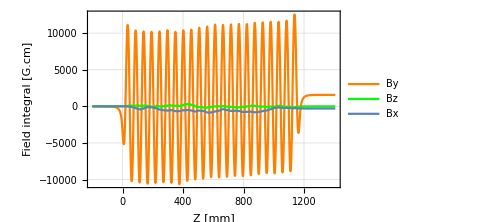

```mathematica
integral1=idFieldInt[device,li,lf,lstep,baxis,display=1,oneplot=1];
```

```mathematica
idFastFirstInt[baxis,li,lf,lstep,"y"]
```

818.834

```mathematica
y=idFieldIntRK[device,lf,li,lstep];
y[[-1,2]]
```

818.437

```mathematica
p1=ListLinePlot[integral1[[1,1;;10,2]],PlotStyle->Black,PlotTheme->"Detailed",PlotRange->{{2000,2180},All}];
p2=ListLinePlot[y[[2;;10,2]],PlotStyle->{Dashed,Red}];
Show[{p1,p2}]
```

### Trajectory

> IDRungeKuttaTrajectory: elapsed time = 84.6020004 s

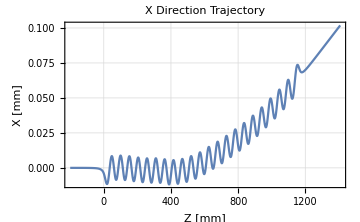
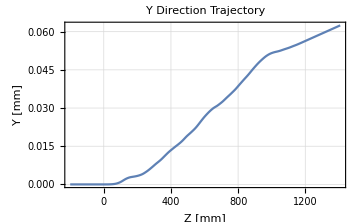

```mathematica
smax=lf;
rkstep=lstep;
r0={0,0,li,0,0,1};

Trajetoria=idTrajectory[device, eEnergy,r0,smax,rkstep,display=1] ;
```

```mathematica
FinalBlockPosition=(0.875*periodL/4)*6+(nPeriods*4+1-1)*periodL/4
```

1171.41

```mathematica
pError=idPhaseError[baxis,li,lf,lNpts,Trajetoria,eEnergy];
```

> Phase solved: elapsed time = 4.2812881[s]

Phase Error: 9.77906[deg]rms

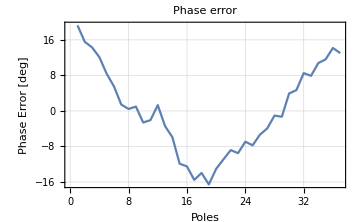

```mathematica
Print["Phase Error: ",RootMeanSquare[pError],"[deg]rms"]

ListLinePlot[pError,Frame->True,FrameLabel->{Style["Poles",12],Style["Phase Error [deg]",12]},PlotLabel->Style["Phase error",Bold,12],PlotTheme->"Detailed",ImageSize->Medium]
```

### Testes New Functions

```mathematica
mag0=idImportMag[typeID,nPeriods=2,fileName="blocks_test.xlsx"]
```

[Error] Insufficient number of blocks for 2 periods.